```mathematica
Exit[]
```

```mathematica
f[x_]:=a x^3+b x^2+c x+d
```

```mathematica
erg=Solve[{f[0]==bounds[1],f[nPoints+1]==bounds[2],f'[nPoints+1]/f'[0]==args[3],},{a,b,c,d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→-(a (1+nPoints) (2+args[3]))/(1+args[3])-((-1+args[3]) (bounds[1]-bounds[2]))/((1+nPoints)^2 (1+args[3])),c→-(a (-1-2 nPoints-nPoints^2))/(1+args[3])-(2 (bounds[1]-bounds[2]))/((1+nPoints) (1+args[3])),d→bounds[1]}}

```mathematica
f[nPoints+1]/f[0]
```

(d+c (1+nPoints)+b (1+nPoints)^2+a (1+nPoints)^3)/d

```mathematica
FortranForm[erg]
```

List(Rule(a,-((-(((1 + nPoints)**2 - 2*(1 + nPoints)*args(1))*(args(2) - args(4))) + 
     -        (-2*args(1) + 2*args(3))*((1 + nPoints)*args(2) + bounds(1) - bounds(2)))/
     -      (((1 + nPoints)**3 - 3*(1 + nPoints)*args(1)**2)*(-2*args(1) + 2*args(3)) - 
     -        ((1 + nPoints)**2 - 2*(1 + nPoints)*args(1))*(-3*args(1)**2 + 3*args(3)**2)))),
     -  Rule(b,-(-args(2) + args(4))/(2.*(args(1) - args(3))) + 
     -    ((-3*args(1)**2 + 3*args(3)**2)*(-(((1 + nPoints)**2 - 2*(1 + nPoints)*args(1))*(args(2) - args(4))) + 
     -         (-2*args(1) + 2*args(3))*((1 + nPoints)*args(2) + bounds(1) - bounds(2))))/
     -     ((-2*args(1) + 2*args(3))*(((1 + nPoints)**3 - 3*(1 + nPoints)*args(1)**2)*(-2*args(1) + 2*args(3)) - 
     -         ((1 + nPoints)**2 - 2*(1 + nPoints)*args(1))*(-3*args(1)**2 + 3*args(3)**2)))),
     -  Rule(c,-((args(2)*args(3) - args(1)*args(4))/(args(1) - args(3))) - 
     -    (3*args(1)*args(3)*(-(((1 + nPoints)**2 - 2*(1 + nPoints)*args(1))*(args(2) - args(4))) + 
     -         (-2*args(1) + 2*args(3))*((1 + nPoints)*args(2) + bounds(1) - bounds(2))))/
     -     (((1 + nPoints)**3 - 3*(1 + nPoints)*args(1)**2)*(-2*args(1) + 2*args(3)) - 
     -       ((1 + nPoints)**2 - 2*(1 + nPoints)*args(1))*(-3*args(1)**2 + 3*args(3)**2))),Rule(d,bounds(1)))

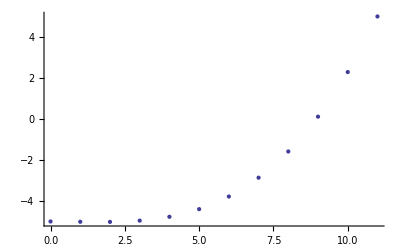

```mathematica
nPoints=10;args[1]=0;args[2]=0;args[3]=11;args[4]=3;bounds[1]=-5;bounds[2]=5;ListPlot[Table[{x,f[x]/.erg},{x,0,nPoints+1}],PlotRange->All]
```

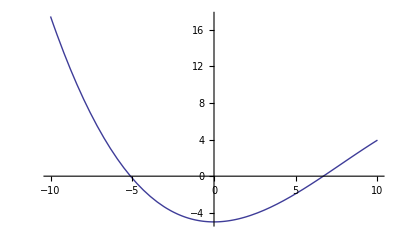

```mathematica
Plot[f[x]/.erg,{x,-10,10}]
```

```mathematica
Table[f[x]/.erg,{x,0,nPoints+1}]//N
```

{-5.,-5.01503,-5.02104,-4.95943,-4.7716,-4.39895,-3.78287,-2.86476,-1.58603,0.111946,2.28775,5.}

```mathematica
Differences[%]
```

{-0.0150263,-0.00601052,0.0616078,0.187829,0.372652,0.616078,0.918107,1.27874,1.69797,2.17581,2.71225}

```mathematica
Exit[]
```

```mathematica
f[x_]:=a x^2+b x+c
```

```mathematica
nPoints=10;args[1]=-5;args[2]=0;args[3]=0.01;bounds[1]=-5;bounds[2]=5;
```

```mathematica
erg1=Solve[{f'[args[1]]==args[2],f'[1]==args[3]},{a,b}][[1]]
```

{a→0.000833333,b→0.00833333}

```mathematica
ii=Integrate[1/f[x]/.erg1,{x,bounds[1],bounds[2]}]
```

ConditionalExpression[(2. ArcTan[0.0166667/(√(-0.0000694444+0.00333333 c))])/(√(-0.0000694444+0.00333333 c)),(Re[√(0.0000694444-0.00333333 c)]≥0.0166667||c>0.0208333||(√(1.-48. c)≠0&&√(0.0000694444-0.00333333 c)∉Reals))&&√(0.0000694444-0.00333333 c)≠0]

```mathematica
erg2=Simplify[NSolve[ii==nPoints+1,c,Reals]][[1]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{c→0.902814}

```mathematica
v={bounds[1]};For[i=1,i≤nPoints+1,i++,
AppendTo[v,v[[i]]+f[v[[i]]]/.erg1/.erg2];
]
```

```mathematica
Integrate[1/f[x]/.erg1/.erg2,{x,bounds[1],bounds[2]}]
```

11.

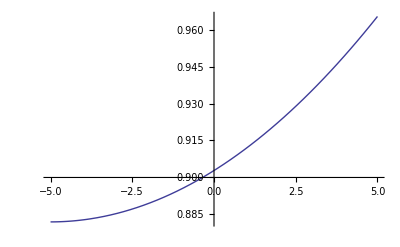

```mathematica
Plot[f[v]/.erg1/.erg2,{v,bounds[1],bounds[2]}]
```

```mathematica
v
```

{-5,-4.11802,-3.23539,-2.35082,-1.46299,-0.570581,0.327749,1.23338,2.14774,3.0723,4.00858,4.95819}

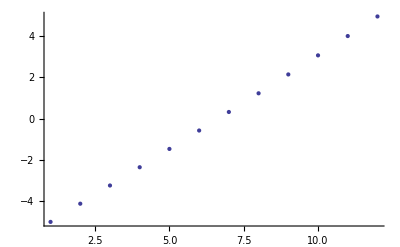

```mathematica
ListPlot[v]
```

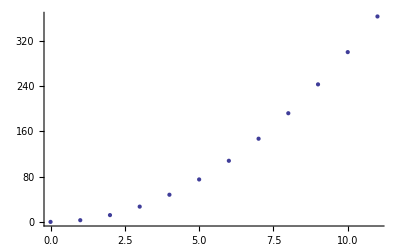

```mathematica
ListPlot[Table[{x,f[x]/.erg1/.erg2},{x,0,nPoints+1}],PlotRange->All]
```

```mathematica
Integrate[1/f[x],{x,-5,5}]/.er
```

$Aborted

```mathematica
Integrate[1/f[x],{x,-5,5}]
```

$Aborted

```mathematica
1/f[x]/.er
```

1/(-4499/90+3 x+6 x^2)

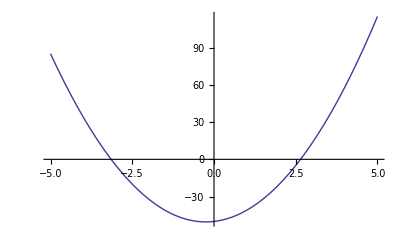

```mathematica
Plot[f[x]/.er,{x,-5,5}]
```

```mathematica
Integrate[1/f[x],{x,,5}]
```

Integrate::idiv: Integral of 1/-4499/90 + 3\ x + 6\ x^2 does not converge on {-5, 5}.

∫_-5^5 1/(-4499/90+3 x+6 x^2)ⅆx

```mathematica
Exit[];
```

```mathematica
Simplify[Integrate[1/f[x],{x,bounds[1],bounds[2]}]]
```

ConditionalExpression[-(2 (ArcTan[(b+2 a bounds[1])/(√(-b^2+4 a c))]-ArcTan[(b+2 a bounds[2])/(√(-b^2+4 a c))]))/(√(-b^2+4 a c)),(Im[bounds[2]] Re[bounds[1]]-Im[bounds[1]] Re[bounds[2]])^2/(Re[bounds[1]]-Re[bounds[2]])^2≤1&&((b-√(b^2-4 a c)+2 a bounds[1])/(2 a bounds[1]-2 a bounds[2])∉Reals||Re[(b-√(b^2-4 a c)+2 a bounds[1])/(2 a bounds[1]-2 a bounds[2])]≥1||Re[(b-√(b^2-4 a c)+2 a bounds[1])/(2 a bounds[1]-2 a bounds[2])]≤0)&&((b+√(b^2-4 a c)+2 a bounds[1])/(2 a bounds[1]-2 a bounds[2])∉Reals||Re[(b+√(b^2-4 a c)+2 a bounds[1])/(2 a bounds[1]-2 a bounds[2])]≥1||Re[(b+√(b^2-4 a c)+2 a bounds[1])/(2 a bounds[1]-2 a bounds[2])]≤0)]

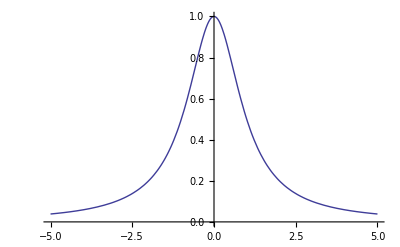

```mathematica
Plot[1/(1+x^2),{x,-5,5}]
```

```mathematica
$Assumptions=a ϵ Reals&&b ϵ Reals
```

a Reals ϵ&&b Reals ϵ

```mathematica
Integrate[1/(x^2+1),{x,a,b}]
```

ConditionalExpression[ArcCot[a]-ArcCot[b],0<a<b]